# Finding ref sequences for A334672

## Implemented and Searched for on OEIS

### All but those with “two repetitions”

{8,11,13,16,23,25,30,31,32,38,39,43,47,49,54,55,56,58,62,63,64,65,67,69,70,71,72,73,77,79,81,82,83,85,88,91,97,98,100,101,103,107,108,109,110,113,114,115,118,121,124,125,128,132,133,139,140,142,143,145,149,151,154,156,157,158,159,161,163,166,168,170,171,172,173,175,176,178,179,181,182,183,184,185,187,189,190,191,193,194,195,198,199,200}

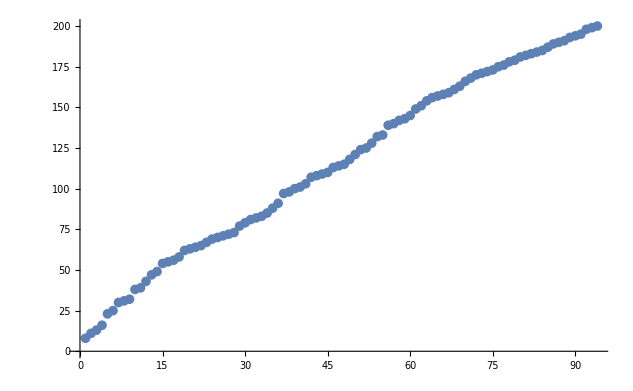

```mathematica
c = 200; rep ={};
Do[(bm = k*2;cR=0;cC=2;dR=1;
While [(cR<bm-1),(
While [(cC<bm),(cR++;If [(cC ==(bm/2+1)),(cC=bm),(cC=(cC-1)*2+1)])];
If [(cC>bm),(cC=2*bm-cC+1;),(cC=2*(bm-cC+1);)];
If[(cC==2),(cR++;If[(cR<bm),dR++;])];
)];
If[dR !=2,AppendTo[rep,k]];
),{k,1,c,1}];
Print[rep];
ListPlot[rep]
```

### Only those with “two repetitions” - https://oeis.org/A238264 - https://oeis.org/A098807 (Numbers 2n arising from A098806.) - https://oeis.org/A098806 (Smallest prime p such that 2n-p and 2n+p are both prime.)

{2,4,6,8,10,12,14,18,20,24,28,30,34,36,38,40,42,44,48,52,54,56,58,66,68,70,72,74,80,82,84,88,90,92,96,100,102,104,106,114,118,120,122,132,136,148,150,152,156,160,168,172,174,178,180,184,186,188,190,192,198,204,208,210,212,222,224,232,234,238,240,244,246,252,254,258,260,262,268,270,272,274,276,282,288,292,294,296,300,304,306,310,320,324,328,330,334,338,348,354,360,372,376,384,392,394}

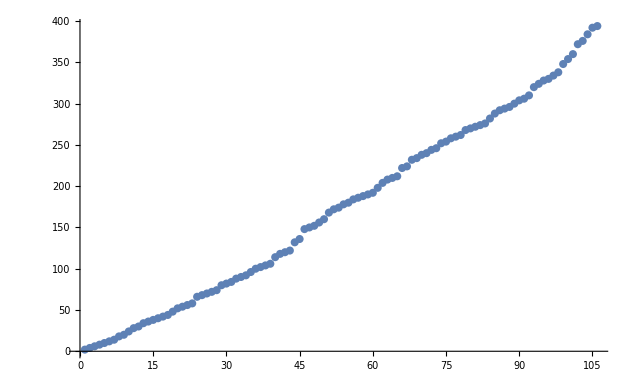

```mathematica
c = 200; rep ={};
Do[(bm = k*2;cR=0;cC=2;dR=1;
While [(cR<bm-1),(
While [(cC<bm),(cR++;If [(cC ==(bm/2+1)),(cC=bm),(cC=(cC-1)*2+1)])];
If [(cC>bm),(cC=2*bm-cC+1;),(cC=2*(bm-cC+1);)];
If[(cC==2),(cR++;If[(cR<bm),dR++;])];
)];
If[dR ==2,AppendTo[rep,2*k]];
),{k,1,c,1}];
Print[rep];
ListPlot[rep]
```

### Only “even repetitions”

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,48,50,51,52,53,54,56,57,58,59,60,61,62,63,64,65,66,68,71,73,74,75,76,77,78,79,80,83,84,86,87,89,90,91,92,93,94,95,96,97,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,115,116,117,119,120,121,122,123,125,126,127,129,130,131,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,150,151,152,153,154,155,156,158,159,160,161,162,164,165,166,167,168,169,170,171,173,174,176,177,179,180,181,182,185,186,187,188,190,192,194,196,197,199}

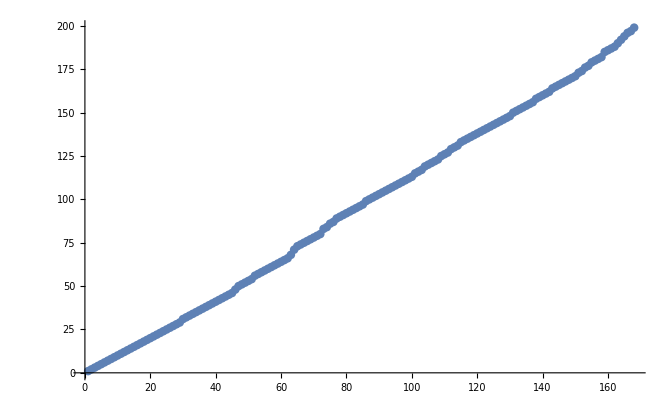

```mathematica
c = 200; rep ={};
Do[
(
bm = k*2;
cR=0;
cC=2;
dR=1;
While [(cR<bm-1),(
While [(cC<bm),(cR++;
If [
(cC ==(bm/2+1)),
(cC=bm),
(cC=(cC-1)*2+1)])
];
If [(cC>bm),(cC=2*bm-cC+1;),(cC=2*(bm-cC+1);)];
If[(cC==2),(cR++;If[(cR<bm),dR++;])];
)];
If[Mod[dR,2]==0,AppendTo[rep,k]];
),{k,1,c,1}];
Print[rep];
ListPlot[rep]
```

### Only “odd repetitions” - https://oeis.org/A306720 (https://oeis.org/A306720)

This need to be thought through. If OEIS can’t find the sequence for n that generates odd numbers, ie, the exceptions are not easy to find.
a(30) gives an odd number a(1) -> a(29) -> even.

Seq:
{30,47,49,55,67,69,70,72,81,82,85,88,98}

Red = even number and in sequence
Blue = Even number and not in sequence

{{1,0},{2,1},{3,1},{4,2},{5,1},{6,1},{7,1},{8,3},{9,1},{10,1},{11,3},{12,1},{13,3},{14,1},{15,1},{16,6},{17,1},{18,1},{19,1},{20,1},{21,1},{22,1},{23,3},{24,1},{25,3},{26,1},{27,1},{28,1},{29,1},{30,2},{31,3},{32,9},{33,1},{34,1},{35,1},{36,1},{37,1},{38,5},{39,3},{40,1},{41,1},{42,1},{43,9},{44,1},{45,1},{46,1},{47,2},{48,1},{49,8},{50,1},{51,1},{52,1},{53,1},{54,3},{55,6},{56,3},{57,1},{58,3},{59,1},{60,1},{61,1},{62,3},{63,5},{64,16},{65,3},{66,1},{67,6},{68,1},{69,6},{70,4},{71,3},{72,2},{73,3},{74,1},{75,1},{76,1},{77,3},{78,1},{79,13},{80,1},{81,2},{82,4},{83,11},{84,1},{85,6},{86,1},{87,1},{88,4},{89,1},{90,1},{91,3},{92,1},{93,1},{94,1},{95,1},{96,1},{97,9},{98,2},{99,1},{100,11}}

{30,47,49,55,67,69,70,72,81,82,85,88,98}

{{1,0},{2,1},{3,1},{4,2},{5,1},{6,1},{7,1},{8,3},{9,1},{10,1},{11,3},{12,1},{13,3},{14,1},{15,1},{16,6},{17,1},{18,1},{19,1},{20,1},{21,1},{22,1},{23,3},{24,1},{25,3},{26,1},{27,1},{28,1},{29,1},{30,2},{31,3},{32,9},{33,1},{34,1},{35,1},{36,1},{37,1},{38,5},{39,3},{40,1},{41,1},{42,1},{43,9},{44,1},{45,1},{46,1},{47,2},{48,1},{49,8},{50,1},{51,1},{52,1},{53,1},{54,3},{55,6},{56,3},{57,1},{58,3},{59,1},{60,1},{61,1},{62,3},{63,5},{64,16},{65,3},{66,1},{67,6},{68,1},{69,6},{70,4},{71,3},{72,2},{73,3},{74,1},{75,1},{76,1},{77,3},{78,1},{79,13},{80,1},{81,2},{82,4},{83,11},{84,1},{85,6},{86,1},{87,1},{88,4},{89,1},{90,1},{91,3},{92,1},{93,1},{94,1},{95,1},{96,1},{97,9},{98,2},{99,1},{100,11}}

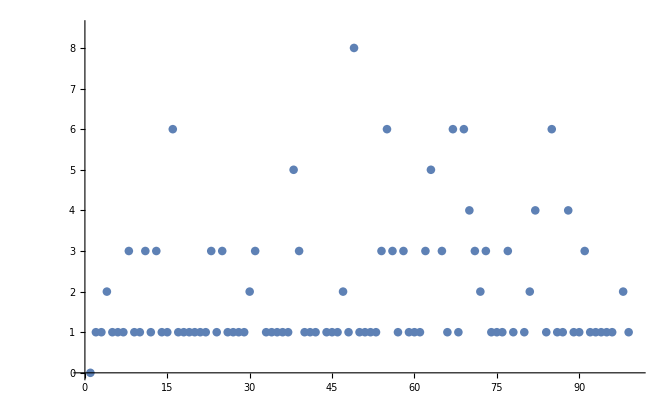

```mathematica
c = 100; 
rep ={};
reHit = {};
Do[(bm = k*2;
cR=0;
cC=2;
dR=1;
hitM= 0;
While [(cR<bm-1),(
While [(cC<bm),(
cR++;
If [(cC ==(bm/2+1)),
(cC=bm; hitM++),
(cC=(cC-1)*2+1)]
)];
If [(cC>bm),(cC=2*bm-cC+1;),(cC=2*(bm-cC+1);)];
If[(cC==2),(cR++;If[(cR<bm),dR++;])];
)];
If[Mod[dR,2]==1,AppendTo[rep,k]; ];
AppendTo[reHit,{k,hitM}]
),{k,1,c,1}];
Print[rep];
Print[reHit];
ListPlot[reHit]
```

## Not Implemented yet

### Only “even acc from prev number”

```mathematica
c = 200; rep ={};
Do[(bm = k*2;cR=0;cC=2;dR=1;
While [(cR<bm-1),(
While [(cC<bm),(cR++;If [(cC ==(bm/2+1)),(cC=bm),(cC=(cC-1)*2+1)])];
If [(cC>bm),(cC=2*bm-cC+1;),(cC=2*(bm-cC+1);)];
If[(cC==2),(cR++;If[(cR<bm),dR++;])];
)];
If[ Length[rep]> 1,AppendTo[rep,k]];
),{k,1,c,1}];
Print[rep];
ListPlot[rep]
```

### Only “repetitions that are squares”

```mathematica
c = 200; rep ={};
Do[(bm = k*2;cR=0;cC=2;dR=1;
While [(cR<bm-1),(
While [(cC<bm),(cR++;If [(cC ==(bm/2+1)),(cC=bm),(cC=(cC-1)*2+1)])];
If [(cC>bm),(cC=2*bm-cC+1;),(cC=2*(bm-cC+1);)];
If[(cC==2),(cR++;If[(cR<bm),dR++;])];
)];
If[ Length[rep]> 1,AppendTo[rep,k]];
),{k,1,c,1}];
Print[rep];
ListPlot[rep]
```